## Trajectories

### unstable orbit χ = +1, α = 1/2

-Graphics3D-

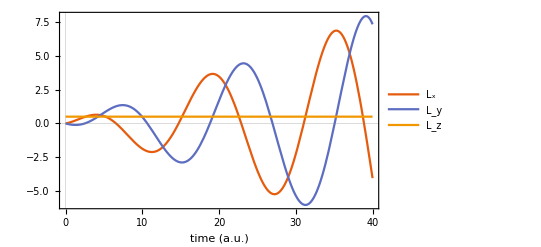

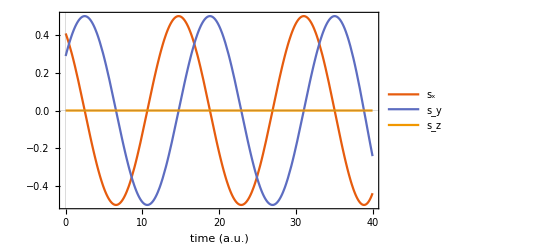

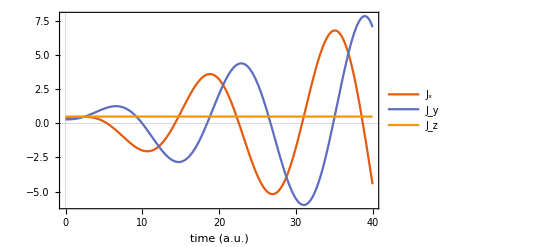

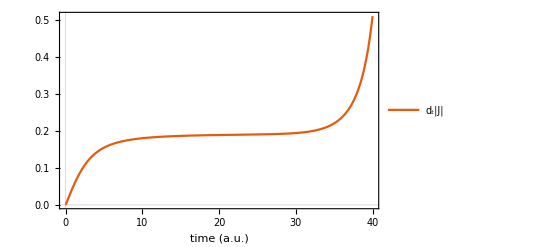

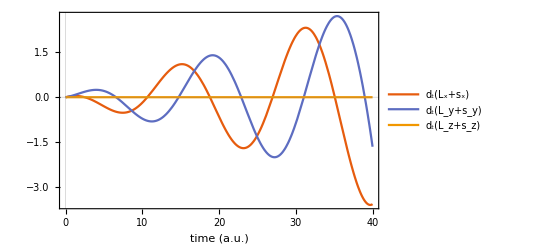

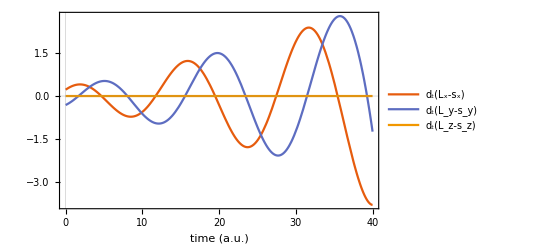

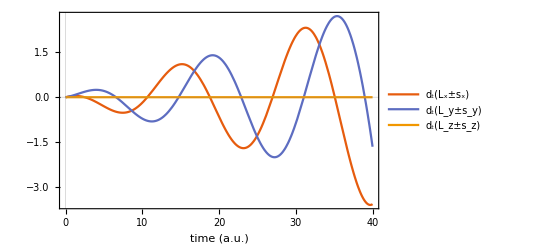

/Users/andreashaller/lensing_device/codes/unstable_orbit_chi_1._alpha_0.5.csv

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=+1;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3,0,0};

(* unstable orbit *)
eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};

Clear[problem,t]
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]

J[t_]:=L[t]+spin[t]

photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->{Front,Right}(*,ViewProjection->"Orthographic"*)]

Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x±s_x)","d_t(L_y±s_y)","d_t(L_z±s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
Graphics3D[Arrow[Tube[tdata]],ViewProjection->"Orthographic"];
Graphics3D[Arrow[Tube[kdata]],ViewProjection->"Orthographic"];
sdata = Table[spin[t],{t,ts}];
dotsdata = Table[spin'[t],{t,ts}];
ldata = Table[L[t],{t,ts}];
dotldata = Table[L'[t],{t,ts}];
jdata = Table[J[t],{t,ts}];
dotjdata = Table[J'[t],{t,ts}];
ListPlot[sdataᵀ,Joined->True,PlotTheme->"Scientific"];
data=Join[{#//N}&/@ts,Table[{χ},{t,ts}],2];
data=Join[data,Table[{α},{t,ts}],2];
data=Join[data,xdata,2];
data=Join[data,dotxdata,2];
data=Join[data,ddotxdata,2];
data=Join[data,kdata,2];
data=Join[data,dotkdata,2];
data=Join[data,ddotkdata,2];
data=Join[data,sdata,2];
data=Join[data,dotsdata,2];
data=Join[data,ldata,2];
data=Join[data,dotldata,2];
data=Join[data,jdata,2];
data=Join[data,dotjdata,2];
header={"t", "\\chi" , "\\alpha" , "x", "y", "z", "\\dot x", "\\dot y", "\\dot z", "\\ddot x", "\\ddot y", "\\ddot z","k_x","k_y","k_z", "\\dot k_x", "\\dot k_y", "\\dot k_z", "\\ddot k_x", "\\ddot k_y", "\\ddot k_z","s_x", "s_y", "s_z","\\dot s_x", "\\dot s_y", "\\dot s_z","L_x","L_y","L_z","\\dot L_x","\\dot L_y","\\dot L_z","J_x","J_y","J_z","\\dot J_x","\\dot J_y","\\dot J_z"};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/unstable_orbit_chi_`1`_alpha_`2`.csv",N[χ],N[α]]],data]
```

### unstable orbit χ = 0, α = 1/2

-Graphics3D-

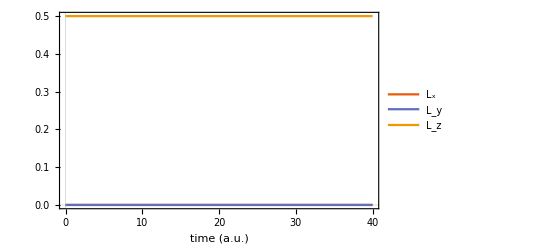

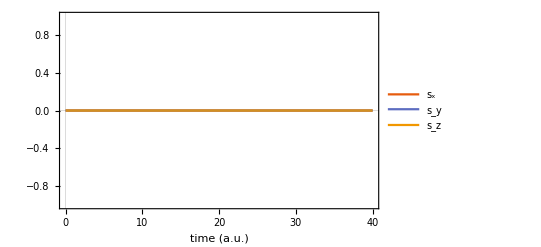

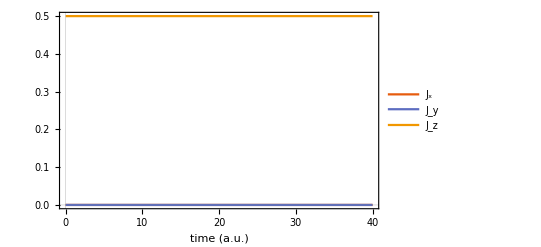

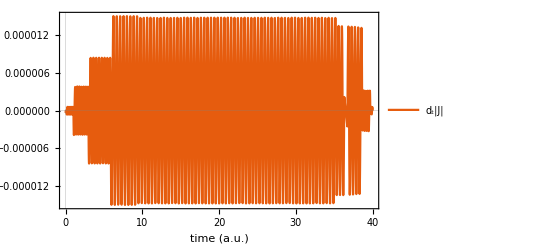

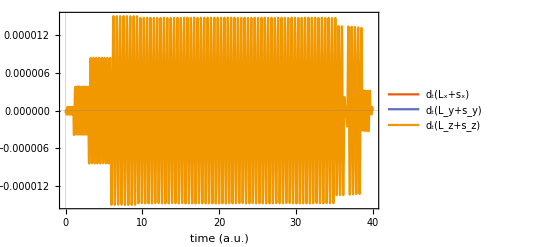

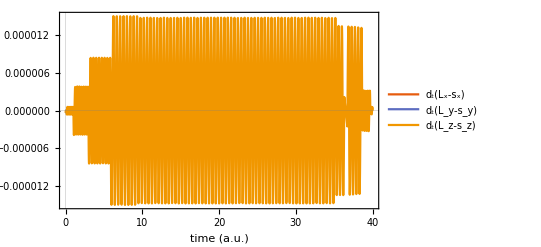

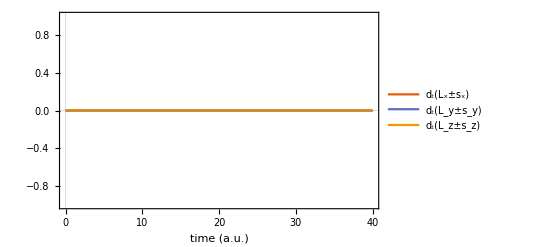

/Users/andreashaller/lensing_device/codes/unstable_orbit_chi_0._alpha_0.5.csv

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=0;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3,0,0};

(* unstable orbit *)
eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};

Clear[problem,t]
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]

J[t_]:=L[t]+spin[t]

photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->{Front,Right}(*,ViewProjection->"Orthographic"*)]

Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x±s_x)","d_t(L_y±s_y)","d_t(L_z±s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
Graphics3D[Arrow[Tube[tdata]],ViewProjection->"Orthographic"];
Graphics3D[Arrow[Tube[kdata]],ViewProjection->"Orthographic"];
sdata = Table[spin[t],{t,ts}];
dotsdata = Table[spin'[t],{t,ts}];
ldata = Table[L[t],{t,ts}];
dotldata = Table[L'[t],{t,ts}];
jdata = Table[J[t],{t,ts}];
dotjdata = Table[J'[t],{t,ts}];
ListPlot[sdataᵀ,Joined->True,PlotTheme->"Scientific"];
data=Join[{#//N}&/@ts,Table[{χ},{t,ts}],2];
data=Join[data,Table[{α},{t,ts}],2];
data=Join[data,xdata,2];
data=Join[data,dotxdata,2];
data=Join[data,ddotxdata,2];
data=Join[data,kdata,2];
data=Join[data,dotkdata,2];
data=Join[data,ddotkdata,2];
data=Join[data,sdata,2];
data=Join[data,dotsdata,2];
data=Join[data,ldata,2];
data=Join[data,dotldata,2];
data=Join[data,jdata,2];
data=Join[data,dotjdata,2];
header={"t", "\\chi" , "\\alpha" , "x", "y", "z", "\\dot x", "\\dot y", "\\dot z", "\\ddot x", "\\ddot y", "\\ddot z","k_x","k_y","k_z", "\\dot k_x", "\\dot k_y", "\\dot k_z", "\\ddot k_x", "\\ddot k_y", "\\ddot k_z","s_x", "s_y", "s_z","\\dot s_x", "\\dot s_y", "\\dot s_z","L_x","L_y","L_z","\\dot L_x","\\dot L_y","\\dot L_z","J_x","J_y","J_z","\\dot J_x","\\dot J_y","\\dot J_z"};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/unstable_orbit_chi_`1`_alpha_`2`.csv",N[χ],N[α]]],data]
```

### unstable orbit χ = -1, α = 1/2

-Graphics3D-

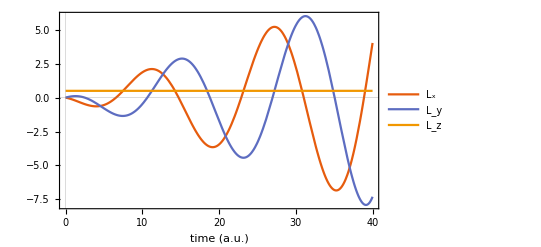

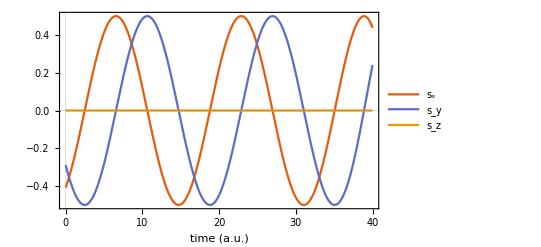

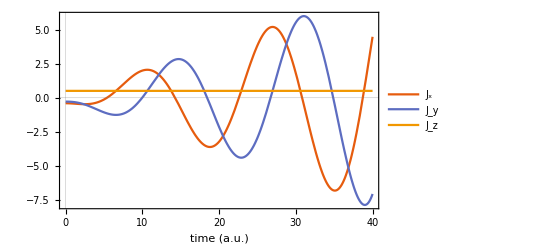

-Graphics-

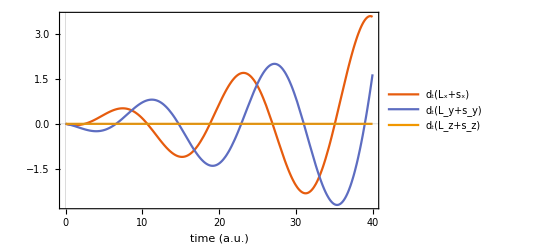

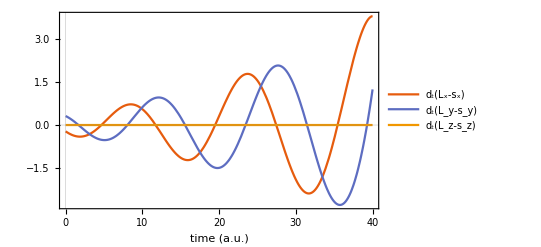

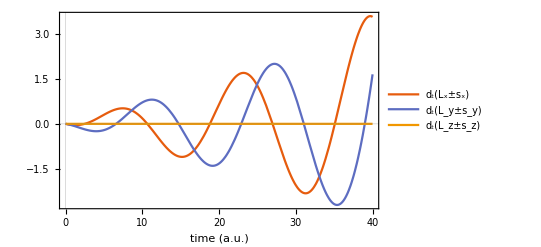

/Users/andreashaller/lensing_device/codes/unstable_orbit_chi_-1._alpha_0.5.csv

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=-1;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3,0,0};

(* unstable orbit *)
eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};

Clear[problem,t]
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]

J[t_]:=L[t]+spin[t]

photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->{Front,Right}(*,ViewProjection->"Orthographic"*)]

Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x±s_x)","d_t(L_y±s_y)","d_t(L_z±s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
Graphics3D[Arrow[Tube[tdata]],ViewProjection->"Orthographic"];
Graphics3D[Arrow[Tube[kdata]],ViewProjection->"Orthographic"];
sdata = Table[spin[t],{t,ts}];
dotsdata = Table[spin'[t],{t,ts}];
ldata = Table[L[t],{t,ts}];
dotldata = Table[L'[t],{t,ts}];
jdata = Table[J[t],{t,ts}];
dotjdata = Table[J'[t],{t,ts}];
ListPlot[sdataᵀ,Joined->True,PlotTheme->"Scientific"];
data=Join[{#//N}&/@ts,Table[{χ},{t,ts}],2];
data=Join[data,Table[{α},{t,ts}],2];
data=Join[data,xdata,2];
data=Join[data,dotxdata,2];
data=Join[data,ddotxdata,2];
data=Join[data,kdata,2];
data=Join[data,dotkdata,2];
data=Join[data,ddotkdata,2];
data=Join[data,sdata,2];
data=Join[data,dotsdata,2];
data=Join[data,ldata,2];
data=Join[data,dotldata,2];
data=Join[data,jdata,2];
data=Join[data,dotjdata,2];
header={"t", "\\chi" , "\\alpha" , "x", "y", "z", "\\dot x", "\\dot y", "\\dot z", "\\ddot x", "\\ddot y", "\\ddot z","k_x","k_y","k_z", "\\dot k_x", "\\dot k_y", "\\dot k_z", "\\ddot k_x", "\\ddot k_y", "\\ddot k_z","s_x", "s_y", "s_z","\\dot s_x", "\\dot s_y", "\\dot s_z","L_x","L_y","L_z","\\dot L_x","\\dot L_y","\\dot L_z","J_x","J_y","J_z","\\dot J_x","\\dot J_y","\\dot J_z"};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/unstable_orbit_chi_`1`_alpha_`2`.csv",N[χ],N[α]]],data]
```

### lensed trajectory χ = 1, α = 1/2

-Graphics3D-

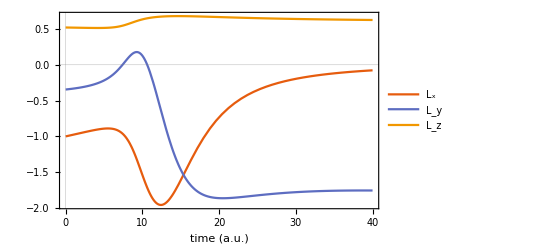

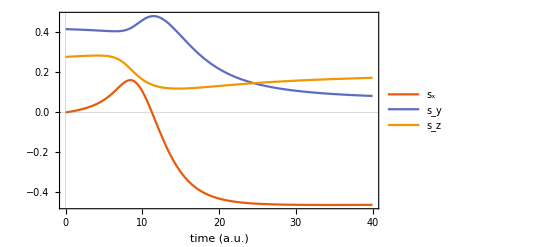

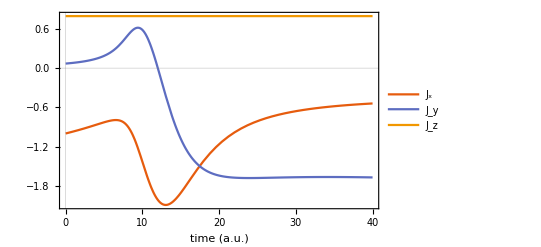

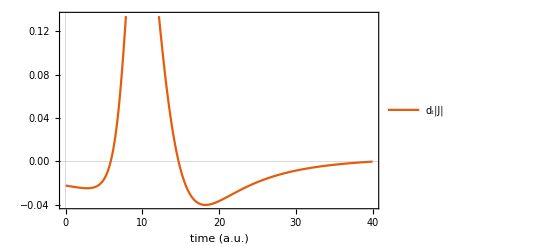

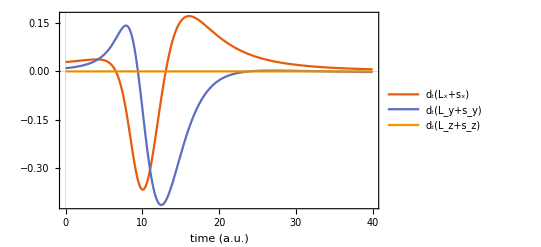

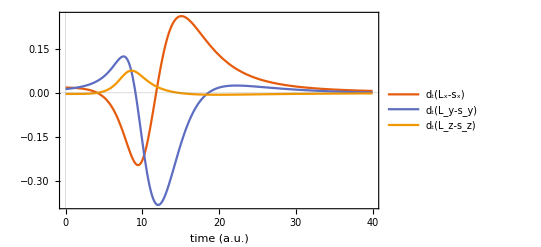

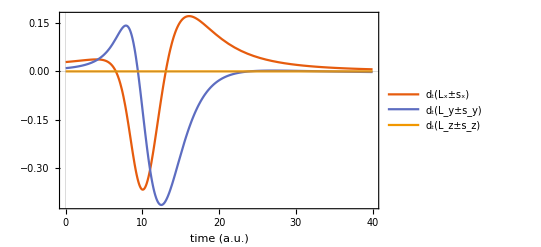

/Users/andreashaller/lensing_device/codes/lensed_trajectory_chi_1._alpha_0.5.csv

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=1;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0.1};
eq3=xv[0]=={3.46,-10,0};

(* unstable orbit *)
(*eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};*)

Clear[problem,t]
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]

J[t_]:=L[t]+spin[t]

photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->Top,ViewProjection->"Orthographic"]

Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x±s_x)","d_t(L_y±s_y)","d_t(L_z±s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
Graphics3D[Arrow[Tube[tdata]],ViewProjection->"Orthographic"];
Graphics3D[Arrow[Tube[kdata]],ViewProjection->"Orthographic"];
sdata = Table[spin[t],{t,ts}];
dotsdata = Table[spin'[t],{t,ts}];
ldata = Table[L[t],{t,ts}];
dotldata = Table[L'[t],{t,ts}];
jdata = Table[J[t],{t,ts}];
dotjdata = Table[J'[t],{t,ts}];
ListPlot[sdataᵀ,Joined->True,PlotTheme->"Scientific"];
data=Join[{#//N}&/@ts,Table[{χ},{t,ts}],2];
data=Join[data,Table[{α},{t,ts}],2];
data=Join[data,xdata,2];
data=Join[data,dotxdata,2];
data=Join[data,ddotxdata,2];
data=Join[data,kdata,2];
data=Join[data,dotkdata,2];
data=Join[data,ddotkdata,2];
data=Join[data,sdata,2];
data=Join[data,dotsdata,2];
data=Join[data,ldata,2];
data=Join[data,dotldata,2];
data=Join[data,jdata,2];
data=Join[data,dotjdata,2];
header={"t", "\\chi" , "\\alpha" , "x", "y", "z", "\\dot x", "\\dot y", "\\dot z", "\\ddot x", "\\ddot y", "\\ddot z","k_x","k_y","k_z", "\\dot k_x", "\\dot k_y", "\\dot k_z", "\\ddot k_x", "\\ddot k_y", "\\ddot k_z","s_x", "s_y", "s_z","\\dot s_x", "\\dot s_y", "\\dot s_z","L_x","L_y","L_z","\\dot L_x","\\dot L_y","\\dot L_z","J_x","J_y","J_z","\\dot J_x","\\dot J_y","\\dot J_z"};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/lensed_trajectory_chi_`1`_alpha_`2`.csv",N[χ],N[α]]],data]
```

### lensed trajectory χ = 0, α = 1/2

-Graphics3D-

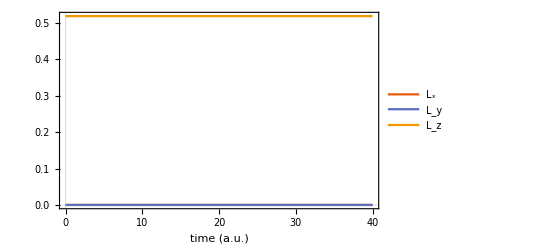

-Graphics-

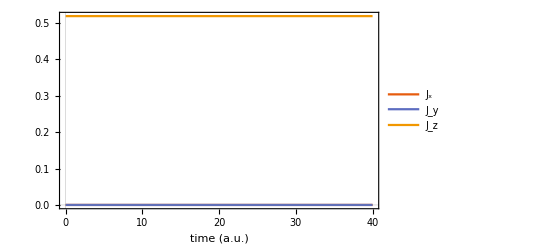

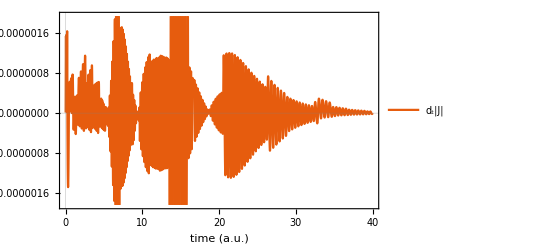

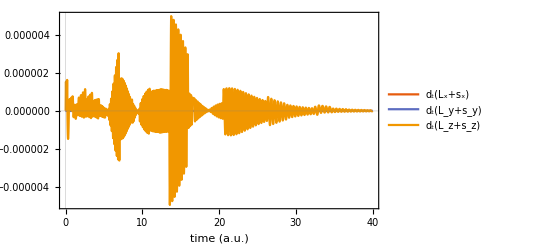

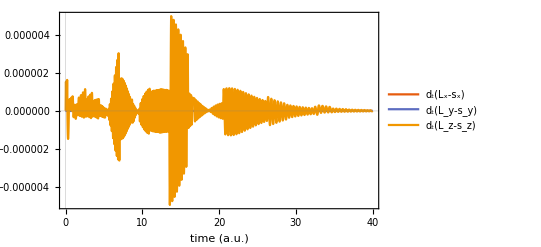

-Graphics-

/Users/andreas.haller/lensing_device/codes/lensed_trajectory_chi_0._alpha_0.5.csv

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=0;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3.46,-10,0};

(* unstable orbit *)
(*eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};*)

Clear[problem,t]
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]

J[t_]:=L[t]+spin[t]

photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->Top,ViewProjection->"Orthographic"]

Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x±s_x)","d_t(L_y±s_y)","d_t(L_z±s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
Graphics3D[Arrow[Tube[tdata]],ViewProjection->"Orthographic"];
Graphics3D[Arrow[Tube[kdata]],ViewProjection->"Orthographic"];
sdata = Table[spin[t],{t,ts}];
dotsdata = Table[spin'[t],{t,ts}];
ldata = Table[L[t],{t,ts}];
dotldata = Table[L'[t],{t,ts}];
jdata = Table[J[t],{t,ts}];
dotjdata = Table[J'[t],{t,ts}];
ListPlot[sdataᵀ,Joined->True,PlotTheme->"Scientific"];
data=Join[{#//N}&/@ts,Table[{χ},{t,ts}],2];
data=Join[data,Table[{α},{t,ts}],2];
data=Join[data,xdata,2];
data=Join[data,dotxdata,2];
data=Join[data,ddotxdata,2];
data=Join[data,kdata,2];
data=Join[data,dotkdata,2];
data=Join[data,ddotkdata,2];
data=Join[data,sdata,2];
data=Join[data,dotsdata,2];
data=Join[data,ldata,2];
data=Join[data,dotldata,2];
data=Join[data,jdata,2];
data=Join[data,dotjdata,2];
header={"t", "\\chi" , "\\alpha" , "x", "y", "z", "\\dot x", "\\dot y", "\\dot z", "\\ddot x", "\\ddot y", "\\ddot z","k_x","k_y","k_z", "\\dot k_x", "\\dot k_y", "\\dot k_z", "\\ddot k_x", "\\ddot k_y", "\\ddot k_z","s_x", "s_y", "s_z","\\dot s_x", "\\dot s_y", "\\dot s_z","L_x","L_y","L_z","\\dot L_x","\\dot L_y","\\dot L_z","J_x","J_y","J_z","\\dot J_x","\\dot J_y","\\dot J_z"};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/lensed_trajectory_chi_`1`_alpha_`2`.csv",N[χ],N[α]]],data]
```

### lensed trajectory χ = -1, α = 1/2

-Graphics3D-

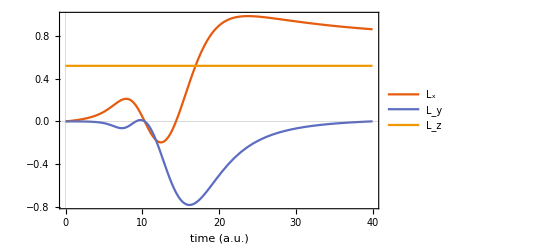

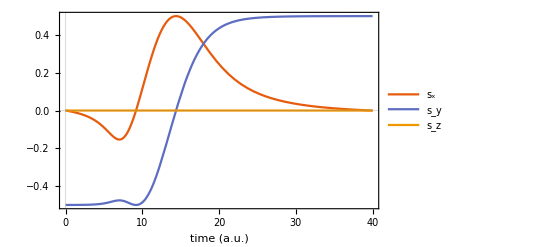

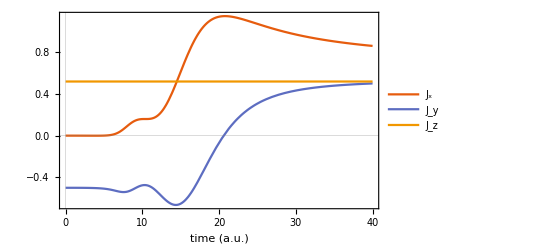

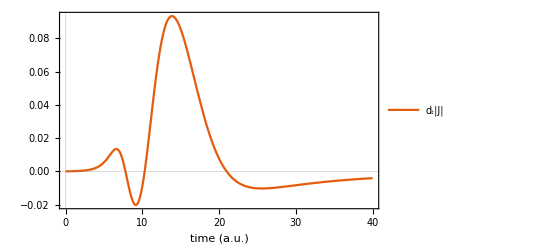

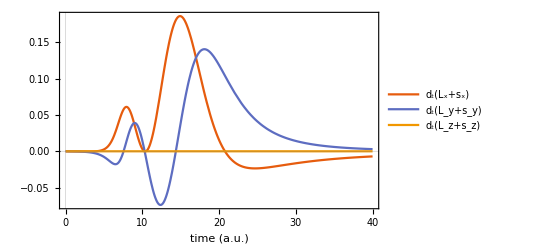

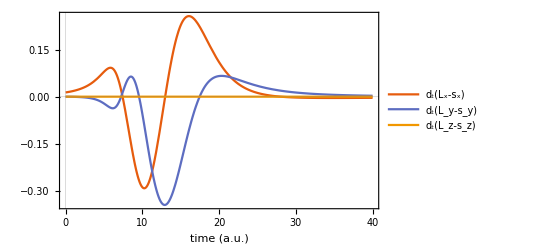

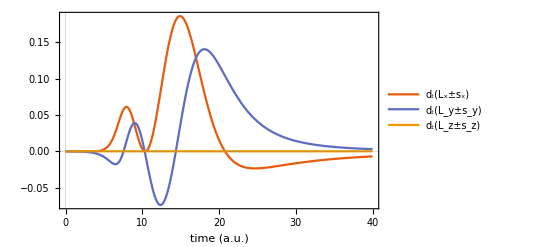

/Users/andreashaller/lensing_device/codes/lensed_trajectory_chi_-1._alpha_0.5.csv

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=-1;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3.46,-10,0};

(* capture *)
(*eq3=xv[0]=={2,-10,0};*)

(* unstable orbit *)
(*eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};*)

Clear[problem,t]
problem[t_]= Join[Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}],{WhenEvent[√(x'[t]^2+y'[t]^2+z'[t]^2)≥10,tf=Min[tf,t];"StopIntegration"]}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]

J[t_]:=L[t]+spin[t]

photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->Top,ViewProjection->"Orthographic"]
Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x±s_x)","d_t(L_y±s_y)","d_t(L_z±s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
Graphics3D[Arrow[Tube[tdata]],ViewProjection->"Orthographic"];
Graphics3D[Arrow[Tube[kdata]],ViewProjection->"Orthographic"];
sdata = Table[spin[t],{t,ts}];
dotsdata = Table[spin'[t],{t,ts}];
ldata = Table[L[t],{t,ts}];
dotldata = Table[L'[t],{t,ts}];
jdata = Table[J[t],{t,ts}];
dotjdata = Table[J'[t],{t,ts}];
ListPlot[sdataᵀ,Joined->True,PlotTheme->"Scientific"];
data=Join[{#//N}&/@ts,Table[{χ},{t,ts}],2];
data=Join[data,Table[{α},{t,ts}],2];
data=Join[data,xdata,2];
data=Join[data,dotxdata,2];
data=Join[data,ddotxdata,2];
data=Join[data,kdata,2];
data=Join[data,dotkdata,2];
data=Join[data,ddotkdata,2];
data=Join[data,sdata,2];
data=Join[data,dotsdata,2];
data=Join[data,ldata,2];
data=Join[data,dotldata,2];
data=Join[data,jdata,2];
data=Join[data,dotjdata,2];
header={"t", "\\chi" , "\\alpha" , "x", "y", "z", "\\dot x", "\\dot y", "\\dot z", "\\ddot x", "\\ddot y", "\\ddot z","k_x","k_y","k_z", "\\dot k_x", "\\dot k_y", "\\dot k_z", "\\ddot k_x", "\\ddot k_y", "\\ddot k_z","s_x", "s_y", "s_z","\\dot s_x", "\\dot s_y", "\\dot s_z","L_x","L_y","L_z","\\dot L_x","\\dot L_y","\\dot L_z","J_x","J_y","J_z","\\dot J_x","\\dot J_y","\\dot J_z"};
data=Prepend[data,header];
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>ToString[StringForm["/lensed_trajectory_chi_`1`_alpha_`2`.csv",N[χ],N[α]]],data]
```

## Lensing angle and Transverse shift

### Lensing Angle

```mathematica
Clear[v,norm,hat,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4,ρm]
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
αs={1/2, 1, 3/2, 2};
allρms={};
allϕs={};
allϕsanalytic={};
allLzs={};
allΔzs={};
alldzdρs={};
Do[
ρm:=(1+α)^(1/(2 α));
u[r_]:=-(1/r)^α;
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*);
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]];

xv[t_]:={x[t],y[t],z[t]};
kv[t_]:={kx[t],ky[t],kz[t]};

Ω[v_]:=1/2 v/norm[v]^3;

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv];
Clear[eq1,eq2,eq3,eq4];
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]-Ω[kv[t]]×kv'[t];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,10,0};

x0s=Table[1.15*Exp[x]ρm,{x,0,4,0.025}];
ϕs={};plots={};ρms={};Lzs={};Δzs={};dzdρs={};kρksqslist={};
Do[
eq3=xv[0]=={x0,1,0};
Clear[problem,t];
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];
ti=-10000;tf=10000;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];
xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;

Clear[L, spin, J];
L[t_]:=xvs[t]×kvs[t];
spin[t_]:=χ/2 hat[kvs[t]];
J[t_]:=L[t]+spin[t];

xvslist = Table[xvs[t],{t,ti,tf,(tf-ti)/1000}];
kvslist = Table[kvs[t],{t,ti,tf,(tf-ti)/1000}];

Lzs =AppendTo[Lzs, L[ti][[3]]];
(*Print[ L[ti][[3]],L[tf][[3]]];*)
Δzs =AppendTo[Δzs,xvs[tf][[3]]-xvs[ti][[3]]];

norms = Norm[#[[;;2]]]&/@xvslist;
AppendTo[ρms,Min[norms]];
p = ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"},ViewPoint->Top];

x1s = {xvs[ti+0.01],xvs[ti]};
x2s ={xvs[tf],xvs[tf-0.01]};

p=Show[p,Graphics3D[Tube[xvslist]]];
(*p = Show[p,Graphics3D[Arrow[Line[{{0,0,0},}]]&/@norms];*)
p = Show[p, Graphics3D[Arrow[Line[#]]&/@{x1s,x2s}]];
p = Show[p,Graphics3D[Sphere[{0,0,0},ρms[[-1]]]],ViewProjection->"Orthographic"];

AppendTo[plots,p];

vecif = Normalize[(Subtract[#[[1]],#[[2]]])]&/@{x1s,x2s};

ϕ=ArcCos[vecif[[1]].vecif[[2]]];
AppendTo[ϕs,ϕ];

Clear[coeff,nint,napprox];
vF=1;
coeff=NIntegrate[(ρ^2-ρm^2 (ρm/ρ)^(2α))/(ρ^2-ρm^2)ρm/(ρ √(ρ^2-ρm^2)),{ρ,ρm,∞}];
nint[ρm_]:=NIntegrate[2 vF/(√(1/ρm^2(vF^2-u[ρm]^2)ρ^4-ρ^2(vF^2-u[ρ]^2))),{ρ,ρm,∞}]-π;
napprox[ρm_]:=coeff (u[ρm]/vF)^2;

Ep=ϵ[xvs[ti],kvs[ti]];
Lz=L[ti][[3]];

ρs=√((#[[1]])^2+(#[[2]])^2)&/@xvslist;
ks=Norm[#]&/@kvslist;

AppendTo[ρslist,ρs];
AppendTo[kslist,ks];

kρksqs = Table[(kvslist[[i]].ρ[xvslist[[i]]])/ks[[i]]^2,{i,Length[ρs]}];

AppendTo[krhoksqs,kρksqs];

dzdρ=-Lz/2 (u'[ρs]-u[ρs]/ρs)/(√(Ep^2 ρs^2-(1-u[ρs]^2)))*kρksqs;

AppendTo[dzdρs, dzdρ];

,{x0,x0s}];
AppendTo[allϕsanalytic,Table[{nint[rhom],napprox[rhom]},{rhom,ρms}]ᵀ];
AppendTo[allϕs,ϕs];
AppendTo[allρms,ρms];
AppendTo[allLzs,Lzs];
AppendTo[allΔzs,Δzs];
AppendTo[alldzdρs,dzdρs];
,{α,αs}]
```

AppendTo::rvalue: kslist is not a variable with a value, so its value cannot be changed.

AppendTo::rvalue: krhoksqs is not a variable with a value, so its value cannot be changed.

AppendTo::rvalue: kslist is not a variable with a value, so its value cannot be changed.

General::stop: Further output of AppendTo::rvalue will be suppressed during this calculation.

$Aborted

```mathematica
.
```

```mathematica
ρms
```

{1.81401,1.8461,1.87924,1.91346,1.94879,1.98525,2.02288,2.06169,2.10172,2.143,2.18555,2.22941,2.2746,2.32117,2.36913,2.41853,2.46939,2.52176,2.57567,2.63114,2.68823,2.74697,2.80739,2.86954,2.93346,2.99918,3.06676,3.13623,3.20765,3.28104,3.35647,3.43399,3.51363,3.59546,3.67951,3.76586,3.85455,3.94564,4.03918,4.13524,4.23387,4.33514,4.43911,4.54585,4.65543,4.76791,4.88336,5.00186,5.12348,5.2483,5.3764,5.50785,5.64274,5.78116,5.92318,6.0689,6.21842,6.37182,6.52919,6.69065,6.85629,7.02621,7.20052,7.37933,7.56275,7.75089,7.94388,8.14183,8.34487,8.55313,8.76673,8.9858,9.2105,9.44095,9.6773,9.9197,10.1683,10.4232,10.6847,10.9529,11.2278,11.5099,11.7991,12.0956,12.3998,12.7117,13.0315,13.3595,13.6958,14.0407,14.3943,14.757,15.1289,15.5102,15.9012,16.3022,16.7134,17.135,17.5673,18.0106,18.4651,18.9312,19.4091,19.8992,20.4017,20.9169,21.4453,21.987,22.5424,23.112,23.696,24.2948,24.9088,25.5384,26.1839,26.8458,27.5245,28.2203,28.9339,29.6655,30.4156,31.1848,31.9734,32.782,33.6111,34.4613,35.3329,36.2267,37.1431,38.0827,39.0461,40.0339,41.0468,42.0853,43.1501,44.2418,45.3612,46.509,47.6859,48.8925,50.1297,51.3983,52.6989,54.0325,55.3999,56.8019,58.2394,59.7133,61.2246,62.7741,64.3628,65.9918,67.662,69.3745,71.1303,72.9307,74.7766,76.6692,78.6098,80.5995,82.6395}

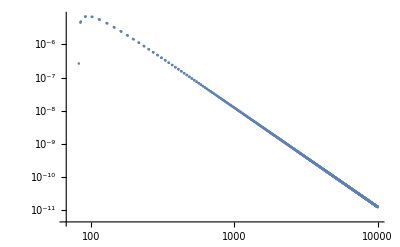

```mathematica
ListLogLogPlot[{ρs,Abs[dzdρ]}ᵀ,PlotRange->Full]
```

```mathematica
<<MaTeX`
```

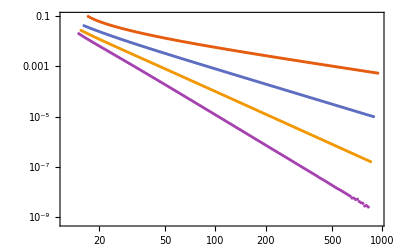

```mathematica
p1=ListLogLogPlot[Table[{allLzs[[i]],-allΔzs[[i]]}ᵀ,{i,Length[allΔzs]}],PlotTheme->"Scientific",FrameLabel->MaTeX[{"L_z","\\Delta z"}]]
```

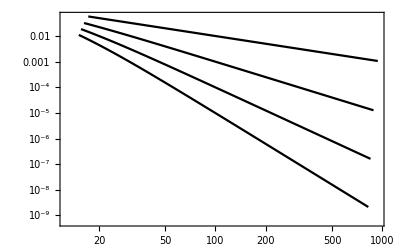

```mathematica
p2=ListLogLogPlot[Table[{allLzs[[i]],(1(*1+αs[[i]]*))/allLzs[[i]](*(√π Gamma[(1+αs[[i]])/2])/Gamma[αs[[i]]/2]*)1/allρms[[i]]^(2αs[[i]]-1)}ᵀ,{i,Length[αs]}],Joined->True,PlotStyle->Black,PlotTheme->"Scientific",FrameLabel->MaTeX[{"L_z","(L_z\\rho^{2\\alpha-1})^{-1}"}]]
```

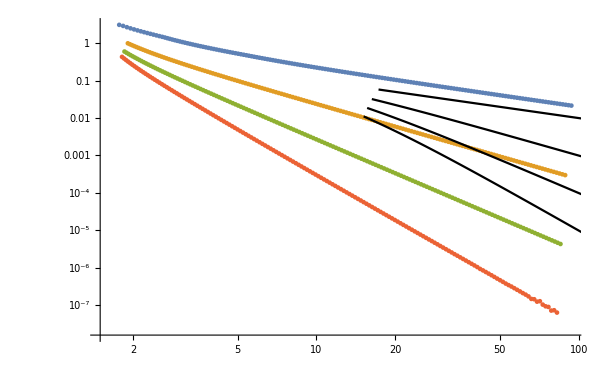

```mathematica
Show[p1,p2]
```

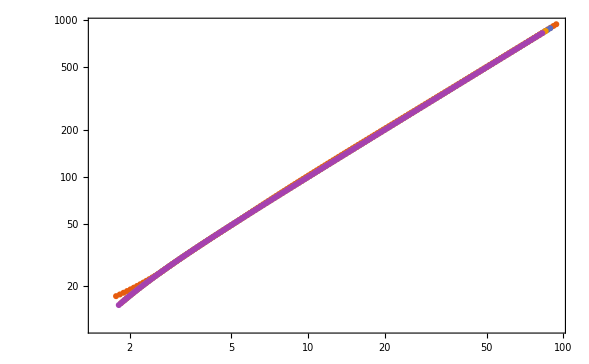

```mathematica
p1=ListLogLogPlot[Table[{allρms[[i]],allLzs[[i]]}ᵀ,{i,Length[allΔzs]}],PlotTheme->"Scientific",FrameLabel->MaTeX[{"\\rho_p","L_z"}]]
```

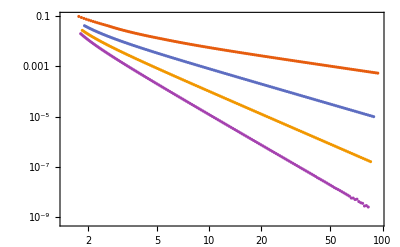

```mathematica
p1=ListLogLogPlot[Table[{allρms[[i]],-allΔzs[[i]]}ᵀ,{i,Length[allΔzs]}],PlotTheme->"Scientific",FrameLabel->MaTeX[{"\\rho_p","(L_z\\rho^{2\\alpha-1})^{-1}"}]]
```

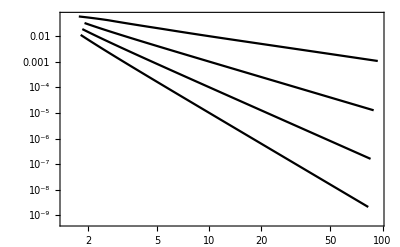

```mathematica
p2=ListLogLogPlot[Table[{allρms[[i]],1/allLzs[[i]]/allρms[[i]]^(2αs[[i]]-1)}ᵀ,{i,Length[αs]}],Joined->True,PlotStyle->Black,PlotTheme->"Scientific",FrameLabel->MaTeX[{"\\rho_p","(L_z\\rho^{2\\alpha-1})^{-1}"}]]
```

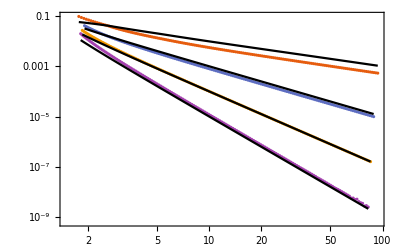

```mathematica
Show[p1,p2]
```

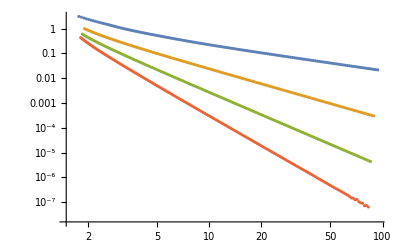

```mathematica
lensingNumeric=Table[{allρms[[i]],Re[allϕs[[i]]]}ᵀ,{i,Length[allϕs]}];
p1=ListLogLogPlot[lensingNumeric]
```

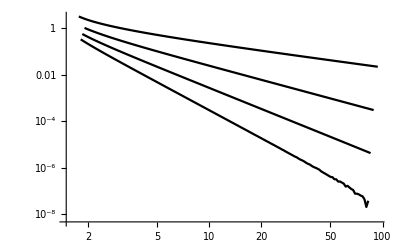

```mathematica
lensingAnalytic=Table[{allρms[[i]],Re[allϕsanalytic[[i,1]]]}ᵀ,{i,Length[allϕs]}];
p2=ListLogLogPlot[lensingAnalytic,Joined->True,PlotStyle->Black]
```

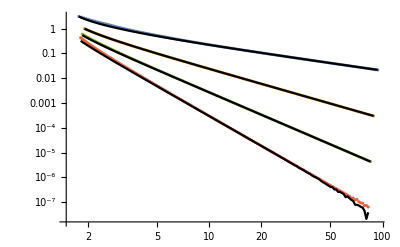

```mathematica
Show[p1,p2]
```

```mathematica
lensingNumerical=Table[{allρms[[i]],allϕs[[i]]}ᵀ,{i,Length[allρms]}];
lensingNumericalMatrix=ArrayReshape[TensorTranspose[lensingNumerical,{2,1,3}],{Length[ρms],8}];
lensingAnalytic1=Table[{allρms[[i]],Re[allϕsanalytic[[i,1]]]}ᵀ,{i,Length[allρms]}];
lensingAnalytic1//Dimensions
lensingAnalyticMatrix1=ArrayReshape[TensorTranspose[lensingAnalytic1,{2,1,3}],{Length[ρms],8}];
lensingAnalytic2=Table[{allρms[[i]],Re[allϕsanalytic[[i,2]]]}ᵀ,{i,Length[allρms]}];
lensingAnalytic2//Dimensions
lensingAnalyticMatrix2=ArrayReshape[TensorTranspose[lensingAnalytic2,{2,1,3}],{Length[ρms],8}];
```

{1,161,2}

{1,161,2}

```mathematica
headers =Flatten[{Table[{"\\rho_m"<>ToString[i],"\\varphi"<>ToString[i]},{i,1,Dimensions[lensingAnalyticMatrix1][[2]]/2}]}];
dataOut=Prepend[lensingAnalyticMatrix1,headers];
pathOut=SetDirectory[NotebookDirectory[]]
dataOut//Dimensions
Export[pathOut<>"/lensing_angle_analytic_nint.csv",dataOut]
```

/Users/andreashaller/lensing_device/codes

{162,8}

/Users/andreashaller/lensing_device/codes/lensing_angle_analytic_nint.csv

```mathematica
headers =Flatten[{Table[{"\\rho_m"<>ToString[i],"\\varphi"<>ToString[i]},{i,1,Dimensions[lensingAnalyticMatrix2][[2]]/2}]}];
dataOut=Prepend[lensingAnalyticMatrix2,headers];
pathOut=SetDirectory[NotebookDirectory[]]
dataOut//Dimensions
Export[pathOut<>"/lensing_angle_analytic_approx.csv",dataOut]
```

/Users/andreashaller/lensing_device/codes

{162,8}

/Users/andreashaller/lensing_device/codes/lensing_angle_analytic_approx.csv

```mathematica
headers =Flatten[{Table[{"\\rho_m"<>ToString[i],"\\varphi"<>ToString[i]},{i,1,Dimensions[lensingNumericalMatrix][[2]]/2}]}];
dataOut=Prepend[lensingNumericalMatrix,headers];
dataOut//Dimensions
pathOut=SetDirectory[NotebookDirectory[]];
Export[pathOut<>"/lensing_angle_numeric.csv",dataOut];
```

{162,8}

### Transverse Shift

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4]
α=1/2;χ=-1;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],0v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv+norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3,-20,0};

(*(* unstable orbit *)
eq3=xv[0]=={(1+α)^(1/(2 α)),0,0};
ky0 =  α/(α+1);
kx0=ky0/(√α);
eq4=kv[0]=={kx0,ky0,0};*)

Clear[problem,t]
problem[t_]= Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}];

ti=0;tf=40;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf}]];

xvs[t_]=xv[t]/.solution;
kvs[t_]=kv[t]/.solution;
Clear[L]
L[t_]:=xvs[t]×kvs[t]
spin[t_]:=χ/2 hat[kvs[t]]
J[t_]:=L[t]+spin[t]
```

NDSolve::ndsz: At t == 22.2663, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {40} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

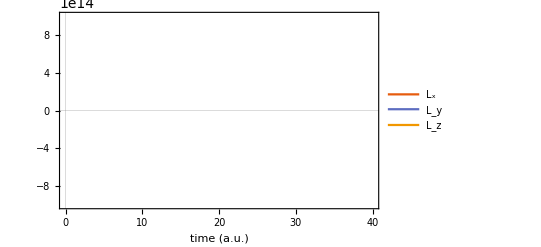

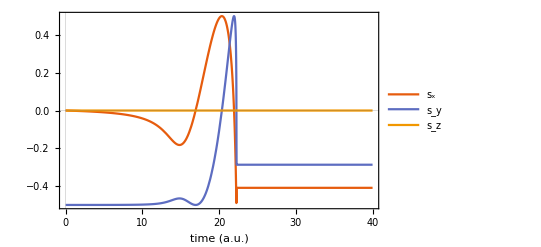

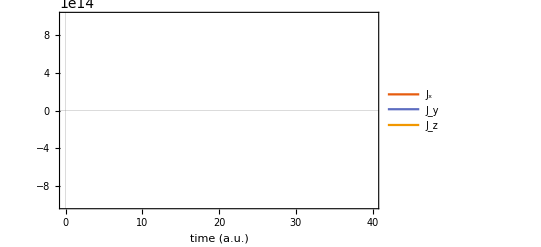

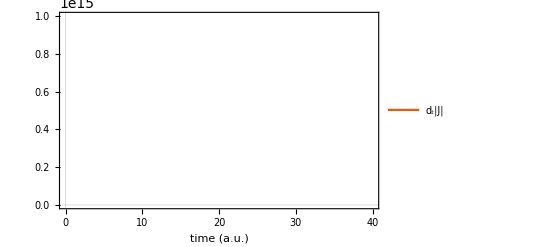

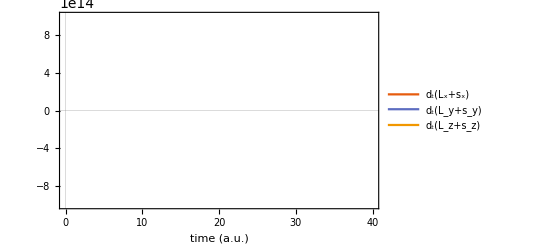

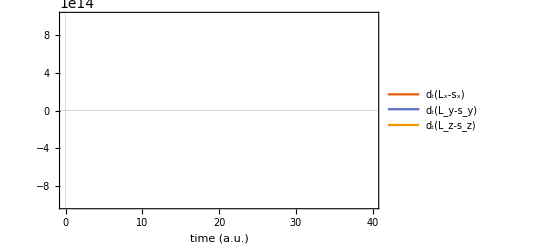

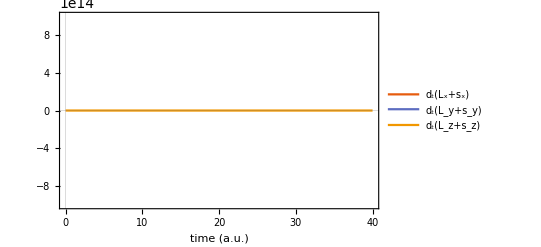

InterpolatingFunction::dmval: Input value {334/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {334/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {334/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {334/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {334/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {334/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];

Show[ParametricPlot3D[Evaluate[xvs[t]],{t,ti,tf},AxesLabel->{"x","y","z"}],Graphics3D[Arrow[Tube[Table[xvs[t],{t,0,1}]]]],inset,ViewPoint->{Front,Right}(*,ViewProjection->"Orthographic"*)]

Plot[Evaluate[L[t]],{t,ti,tf},PlotLegends->{"L_x","L_y","L_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[spin[t]],{t,ti,tf},PlotLegends->{"s_x","s_y","s_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L[t]+spin[t]],{t,ti,tf},PlotLegends->{"J_x","J_y","J_z"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[D[norm[L[ta]-spin[ta]],ta]/.{ta->t},{t,ti,tf},PlotLegends->{"d_t|J|"},PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]+spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Plot[Evaluate[L'[t]-spin'[t]],{t,ti,tf},PlotLegends->{"d_t(L_x-s_x)","d_t(L_y-s_y)","d_t(L_z-s_z)"},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""}]

Jdot[t_]:=-u'[norm[ρ[xvs[t]]]](kvs[t].hat[ρ[xvs[t]]])(xvs[t]×hat[ρ[xvs[t]]])+u[norm[ρ[xvs[t]]]]/norm[ρ[xvs[t]]](ρ[xvs[t]×(kvs[t]-ρ[kvs[t]])] + hat[ρ[xvs[t]]](xvs[t].(hat[ρ[xvs[t]]]×ρ[kvs[t]])))

Plot[Evaluate[Jdot[t]],{t,ti,tf},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"time (a.u.)",""},PlotLegends->{"d_t(L_x+s_x)","d_t(L_y+s_y)","d_t(L_z+s_z)"}]

ts = Range[ti,tf,(tf-ti)/300];
xdata=Table[xvs[t],{t,ts}];
dotxdata=Table[xvs'[t],{t,ts}];
ddotxdata=Table[xvs''[t],{t,ts}];
kdata=Table[kvs[t],{t,ts}];
dotkdata=Table[kvs'[t],{t,ts}];
ddotkdata=Table[kvs''[t],{t,ts}];
```

## Separatrix visualization

### spherical symmetry χ = +1, α = 1/2

```mathematica
Clear[v,norm,hat,α,χ,u,r,ρ,uv,xv,kv,Ω,ϵ,α,kx0,ky0,eq1,eq2,eq3,eq4,ti,tf]
α=1/2;χ=+1;
norm[v_]:=√(v.v)
hat[v_]:=v/norm[v]
u[r_]:=-(1/r)^α
ρ[v_]:={v[[1]],v[[2]],v[[3]]} (* sph.<->cyl. : 0v[[3]] <-> v[[3]]*)
uv[v_]:=u[norm[ρ[v]]]*hat[ρ[v]]

xv[t_]:={x[t],y[t],z[t]}
kv[t_]:={kx[t],ky[t],kz[t]}

Ω[v_]:=χ/2 v/norm[v]^3

ϵ[xv_,kv_]:=uv[ρ[xv]].kv + norm[kv]
Clear[eq1,eq2,eq3,eq4]
eq1 =xv'[t]==+D[ϵ[xv[t],kv[t]],{kv[t],1}]+kv'[t]×Ω[kv[t]];
eq2 =kv'[t]==-D[ϵ[xv[t],kv[t]],{xv[t],1}];

(* lensing trajectory *)
eq4=kv[0]=={0,0.15,0};
eq3=xv[0]=={3,0,0};

lbox=3; xshift={3*lbox,0,0};
x0s =Flatten[Table[{x0,y0,z0}-xshift,{x0,-lbox,lbox},{y0,-lbox,lbox},{z0,{0}}],2];
Do[
eq3=xv[0]==x0s[[indx0]];
eq4=kv[0]=={0,0,-1};

Clear[problems,t];
problem[t_]= Join[Flatten[Table[#[[1,j]]==#[[2,j]],{j,Length[#[[1]]]}]&/@{eq1,eq2,eq3,eq4}],{WhenEvent[√(x'[t]^2+y'[t]^2+z'[t]^2)≥10,tf[indx0]=Min[tf[indx0],t];"StopIntegration"]}];
ti=0;tf[indx0]=4000;

solution=First[NDSolve[problem[t],Flatten[{xv[t],kv[t]}],{t,ti,tf[indx0],0.1}]];
xvs[indx0,t_]=xv[t]/.solution;
kvs[indx0,t_]=kv[t]/.solution;
Clear[L];
L[indx0,t_]:=xvs[t]×kvs[t];
spin[indx0,t_]:=χ/2 hat[kvs[t]];
J[indx0,t_]:=L[t]+spin[t];
,{indx0,Length[x0s]}]
```

```mathematica
tfmax=Max[Table[tf[i],{i,Length[x0s]}]];
photonSphere=Graphics3D[Sphere[{0,0,0},#]&/@{1,(1+α)^(1/(2α))}];
photonCylinder=Graphics3D[Cylinder[{0,0,xvs[#][[3]]}&/@{ti,tf},#]&/@{1,(1+α)^(1/(2α))}];

If[ρ[{0,0,1}][[3]]==1,inset=photonSphere,inset=photonCylinder];
lines = Table[{RandomColor[],Line[Table[xvs[i,t],{t,ti,tf[i]}]]},{i,Length[x0s]}];
```

```mathematica
Graphics3D[lines,ViewPoint->Bottom,PlotRange->{{-1,1},{-1,1},{-1,1}}10]
```

-Graphics3D-